## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`';
Get["MASSef`"];
Get["MASSef`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
rxnName="GAPD";
fitLabel=rxnName;
dataFileName=rxnName;
KeqEquilibrator=0.408;

(* user will need to change this path *)
pathMASSFittingPackage = "/home/mrama/Dropbox/test bla/MASSef/";

mainFolder = "fit_param_scan";
{workingDir, pathData, runFitScriptPath, inputPath, outputPath, bigg2equilibrator}=initializeNotebook[pathMASSFittingPackage, mainFolder];
```

/home/mrama/Dropbox/test bla/MASSef/data

Working dir:/home/mrama/Dropbox/test bla/MASSef/examples/

## Import Data

```mathematica
enzymeDataPath = FileNameJoin[{pathData, "kinetic_data.csv"}, OperatingSystem->$OperatingSystem];
bufferInfoDataPath = FileNameJoin[{pathData, "buffer_info.csv"}, OperatingSystem->$OperatingSystem];
ionChargeDataPath = FileNameJoin[{pathData, "ion_charge.csv"}, OperatingSystem->$OperatingSystem];

{rxn, mechanism, structure, nActiveSites, nAllostericSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}=getEnzymeData[rxnName, enzymeDataPath];

bufferInfo = getBufferInfoData[bufferInfoDataPath];
ionCharge = getIonData[ionChargeDataPath];

inhibitorMet={};
affectedMets={};(*There can be multiple metabolites*)
```

## Construct Module and Set Up Comparison Equations

```mathematica
printEnzymeData[rxn, mechanism, structure, nActiveSites, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi; [nad,g3p,pi,13dpg,nadh]

Structure: 4

Active sites: 4

Km Values:

Substrate | Km_Value | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
nad | 0.000045 | pi | 0.053
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 | 
g3p | 0.00089 | nad | 0.0045
pi | 0.053 | M | 8.9 | 22 | teoa | 0.04 | 
pi | 0.00053 | nad | 0.0045
g3p | 0.089 | M | 8.9 | 22 | teoa | 0.04 |

S0.5 Values:

Substrate | S0.5_Value | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Metabolite(s) | Value | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
g3p | Null
nad | Null
pi | Null | 268 | 1/s | 8.9 | 22 | teoa | 0.04 |

Inhibition Values:

Parameter_Type | Inhibitor | Value | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Parameter_Type | Activator | Value | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Parameter_Type | Metabolite | Value | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
Kd | nad | 3.2×10^-7 | M | 8.9 | 22 | teoa | 0.04 |

### Construct enzyme module

(g3p^c+nad^c+pi^c⇌(13dpg)^c+h^c+nadh^c)^GAPD

Ordered Sequential Bi Bi
"[nad,g3p,pi,1,3-diphosphoglycerate,nadh]"

```mathematica
catalyticBranch={"E_GAPD[c] + nad[c] <=> E_GAPD[c]&nad",
				"E_GAPD[c]&nad + g3p[c] <=> E_GAPD[c]&nad&g3p",
				"E_GAPD[c]&nad&g3p + pi[c] <=> E_GAPD[c]&nad&g3p&pi",
				"E_GAPD[c]&nad&g3p&pi <=> E_GAPD[c]&nadh&13dpg",
				"E_GAPD[c]&nadh&13dpg <=> E_GAPD[c]&nadh + 13dpg[c]",
				"E_GAPD[c]&nadh<=> E_GAPD[c] + nadh[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
```

### Setup King-Altmann Equations

```mathematica
{reverseZeroSub, forwardZeroSub, metSatForSub, metSatRevSub} = getMetsSub[rxn];
rates = getEnzymeRates[enzymeModel];
{KeqName, KeqVal, volumeSub} = getMisc[enzymeModel, rxnName];

(*competitiveRxns={};(*Initialization for later. Do not modify this*)
eqRateConstSub={};(*Initialization for later. Do not modify this*)*)

(*You could modify these, but you shouldn't unless you run into problems*)

lowerParamBound=-6;
upperParamBound=9;
simplifyMaxTime=1*^-5;

(*Extract Transition ID from Mass Action Equations and Separate Catalytic and Non-Catalytic Reactions*)
(*The transition indices are extracted based off of the sum of their mass action stoichiometry.Reactions with a sum of zero are assumed to be catalytic.*)

(*Separate Catalytic and Non-Catalytic Reactions*)
{allCatalyticReactions, nonCatalyticReactions}=classifyReactions[enzymeModel];


(*Identify Transition Rate Equations*)
transitionID =getTransitionIDs[allCatalyticReactions];

(*Extract Transition Rate Equations*)
transitionRateEqs=getTransitionRateEqs[transitionID, rates];

unifiedRateConstList=getUnifiedRateConstList[allCatalyticReactions, nonCatalyticReactions];


(* semi-automated add competitive inhibition steps - none in this enzyme*)
eqRateConstSub={};


(*King-Altman Workaround UsingMathematicaSolve*)
(*This section of code will check to see if there is a 'absoluteFlux.m' file in the notebook directory from a previous cell evalution, and it will either derive a generalized flux equation (may take a long time) or import the previously derived flux equation. Note: If you modify the binding mechanism used in the constructEnzymeModule or manually add additional reactions to the model, you should delete the 'absoluteFlux.m' file in this notebook's current directory.*)
simplifyMaxTime = 100; (*in seconds*)
absoluteFlux=getFluxEquation[inputPath, rxnName, enzymeModel, unifiedRateConstList, transitionRateEqs, nActiveSites, simplifyMaxTime];


(*Equivalent Rate Constant Substitution for Random Ordered Mechanisms*)
(*This should work automatically,a substitution rule list is created with the name:'eqRateConstSub'.It is kind of a greedy section of code,so double check the results to make sure they're accurate*)
eqRateConstSub=getRateConstSubRandomMech[enzymeModel, eqRateConstSub, allCatalyticReactions, nonCatalyticReactions];

(*Assemble Kinetic MASS Action Comparision Equations that Match to Km and kcat Data*)
(*Simplify fixes Python evaluation issues dealing with fractional exponents (e.g.'(-1)**(3/5)' returns 1.0)*)
{absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse}=getRateEqs[absoluteFlux, unifiedRateConstList, eqRateConstSub, reverseZeroSub, forwardZeroSub, volumeSub, metSatForSub, metSatRevSub];


(*Assemble Rate Constant And Metabolite Substitutions for Export*)
{finalRateConsts,metsFull, metsSub, rateConstsSub}=getMetRatesSubs[enzymeModel, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse,KeqVal];

(*Export Equations*)
{eqnNameList, eqnValList, eqnValListPy, fileList, fileListSub}=exportRateEqs[inputPath, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, metsSub, metSatForSub, metSatRevSub, rateConstsSub];
```

## Semi-Automated Simulate Data

### User Input Section

```mathematica
logStepSize=0.2;
(*nonKmParamWeight=3;*)
(*Weighting factor for non-Km data points. You can be specify this manually*)
{minPsDataVal, maxPsDataVal}= getMinMaxPsDataVal[1];
nonKmParamWeight=Length[Table[1,{i,minPsDataVal, maxPsDataVal,logStepSize}]];
eTotal=1;(*Enzyme Total, Should Be 1 for Fitting*)
assumedSaturatingConc=0.01 ;(*in Molarity*)

(*Chemical Activity Correction Options*)
inVivoPH=7.5;(*Assumed in vivo pH*)
inVivoIS=0.25;(*Assumed in vivo Ionic Strength, in Molarity*)
effectiveIonDiameter=3;(*Used in Debye-Huckel equation, in Angstroms*)

(*Initialization of Chemical Activity Correction. These values represent no correction (i.e. Chemical Activity is just the Metabolite Concentration)*)
activeIsoSub=Thread[metsFull->metsFull];(*[S^z] = [S] *)
activityCoefficient=Thread[metsFull->1];(* γ = 1 *)
```

### Simulate data

```mathematica
pHandT={8.9, 22};

kmFittingData= simulateKmData[rxn, metsFull,  metSatForSub, metSatRevSub, kmList, otherParmsList, assumedSaturatingConc, eTotal,
			   logStepSize,activeIsoSub, bufferInfo, ionCharge, inputPath,  fileList, KeqEquilibrator];


kcatFittingData=simulateKcatData[rxn, metsFull,  metSatForSub, metSatRevSub, kcatList, otherParmsList, assumedSaturatingConc, eTotal,
			  logStepSize, nonKmParamWeight, activeIsoSub, bufferInfo, ionCharge, inputPath, 
			  fileList, KeqEquilibrator];


haldane=haldaneRelation[KeqName,allCatalyticReactions]/.unifiedRateConstList;
haldaneRatio=haldane[[2]];

{KeqFittingData, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy}=simulateRateConstRatiosData[haldaneRatio,KeqEquilibrator, KeqEquilibrator, metsFull, rateConstsSub, metsSub, eTotal, nonKmParamWeight, inputPath, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy, pHandT,"haldaneRatio"];


KdRatio=Subscript[k, GAPD1]^⟵/Subscript[k, GAPD1]^⟶;
KdVal=otherParmsList[[1]][[3]];
{KdFittingData, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy}=simulateRateConstRatiosData[KdRatio,KdVal, KeqEquilibrator, metsFull, rateConstsSub, metsSub, eTotal, nonKmParamWeight, inputPath, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy, pHandT, "KdRatio"];


dKdVal =4.25*10^2(*1.92*10^4*);
dKdRatio =(Subscript[k, GAPD1]^⟶Subscript[k, GAPD2]^⟶Subscript[k, GAPD3]^⟶Subscript[k, GAPD4]^⟶Subscript[k, GAPD5]^⟶)/(Subscript[k, GAPD1]^⟵Subscript[k, GAPD2]^⟵Subscript[k, GAPD3]^⟵Subscript[k, GAPD4]^⟵Subscript[k, GAPD5]^⟵);

{dKdFittingData, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy}=simulateRateConstRatiosData[dKdRatio,dKdVal, KeqEquilibrator, metsFull, rateConstsSub, metsSub, eTotal, nonKmParamWeight, inputPath, fileList, fileListSub, eqnNameList, eqnValList, eqnValListPy, pHandT, eqnName="dKdRatio"];
```

### Assemble and export All Data

```mathematica
header=Join[Map[ToString, metsSub[[All,1]]],{"FileFlag", "Target_Data"}];

fittingData = Flatten[{kmFittingData,kcatFittingData, KdFittingData,KeqFittingData,dKdFittingData}, 1];

dataPath =FileNameJoin[{inputPath,dataFileName <>".dat"}, OperatingSystem->$OperatingSystem];

vList=Join[{header},fittingData];
Export[dataPath,vList,"Table"];
FilePrint[dataPath]
```

Keq_GAPD	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0.408	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0.408	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt"	0.13680688860321014
0.408	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt"	0.20076000891310194
0.408	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt"	0.28474724895080133
0.408	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt"	0.386863179846857
0.408	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt"	0.5000000000000002
0.408	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0.408	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt"	0.7152527510491989
0.408	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0.408	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0.408	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_nad.txt"	0.9090909090909093
0.408	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt"	0.090909090909091
0.408	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt"	0.1368068886032102
0.408	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt"	0.2007600089131019
0.408	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt"	0.2847472489508017
0.408	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt"	0.3868631798468571
0.408	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt"	0.5000000000000003
0.408	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt"	0.6131368201531434
0.408	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt"	0.7152527510491988
0.408	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt"	0.7992399910868984
0.408	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt"	0.86319311139679
0.408	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_g3p.txt"	0.9090909090909092
0.408	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt"	0.09090909090909094
0.408	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt"	0.13680688860321008
0.408	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt"	0.20076000891310175
0.408	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt"	0.2847472489508015
0.408	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt"	0.3868631798468569
0.408	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt"	0.5
0.408	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0.408	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt"	0.7152527510491988
0.408	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0.408	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt"	0.8631931113967899
0.408	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/relRateFor_pi.txt"	0.9090909090909092
0.408	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt"	268
0.408	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt"	268
0.408	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt"	268
0.408	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt"	268
0.408	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt"	268
0.408	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt"	268
0.408	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt"	268
0.408	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt"	268
0.408	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt"	268
0.408	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt"	268
0.408	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/absRateFor.txt"	268
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt"	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt"	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt"	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt"	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt"	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt"	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt"	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt"	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt"	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt"	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/KdRatio.txt"	3.2e-7
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt"	0.408
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt"	0.408
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt"	0.408
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt"	0.408
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt"	0.408
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt"	0.408
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt"	0.408
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt"	0.408
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt"	0.408
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt"	0.408
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/haldaneRatio.txt"	0.408
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt"	425.
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt"	425.
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt"	425.
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt"	425.
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt"	425.
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt"	425.
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt"	425.
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt"	425.
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt"	425.
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt"	425.
0.408	0	0	0	0	0	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_dKd_GAPD/input/dKdRatio.txt"	425.

## Generate data for parameter scan

```mathematica
Get["MASSef`"];
Get["MASSef`"];
simulateDataFunctionArguments={rxn, metsFull,  metSatForSub, metSatRevSub, kmList, otherParmsList, assumedSaturatingConc, eTotal,
			   logStepSize,activeIsoSub, bufferInfo, ionCharge, inputPath,  fileList, KeqEquilibrator};

dataType="Km"; (* possible values: "Km", "s05", "kcat", "inhib", "ratio" *)
dataList = kmList;
dataEntry = 1;
remainingFittingDataset = {kcatFittingData, KeqFittingData,KdFittingData, dKdFittingData};
newValuesList = {0.001, 1, 10};
{dataPathList,labelList} = simulateParameterScanData[inputPath, dataType, dataList, dataEntry, newValuesList, remainingFittingDataset, dataFileName, metsSub, simulateDataFunctionArguments];
```

```mathematica
labelList
```

{_Km_1_0.001.dat,_Km_1_1.dat,_Km_1_10.dat}

```mathematica
dataPathList
```

{/home/mrama/Dropbox/test bla/MASSef/examples/fit_param_scan/input/GAPD_Km_1_0.001.dat,/home/mrama/Dropbox/test bla/MASSef/examples/fit_param_scan/input/GAPD_Km_1_1.dat,/home/mrama/Dropbox/test bla/MASSef/examples/fit_param_scan/input/GAPD_Km_1_10.dat}

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=1;
{psoParameterPath,psoResultsFileName, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFileName} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	1
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_param_scan/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_param_scan/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_param_scan/input/relRateFor_g3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_param_scan/input/relRateFor_nad.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_param_scan/input/relRateFor_pi.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_param_scan/input/relRateRev_13dpg.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_param_scan/input/relRateRev_nadh.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_param_scan/input/haldaneRatio.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_param_scan/input/KdRatio.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_param_scan/input/dKdRatio.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_param_scan/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_param_scan/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_param_scan/input/relRateFor_g3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_param_scan/input/relRateFor_nad.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_param_scan/input/relRateFor_pi.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_param_scan/input/relRateRev_13dpg.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_param_scan/input/relRateRev_nadh.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_param_scan/input/haldaneRatio.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_param_scan/input/KdRatio.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_param_scan/input/dKdRatio.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

### Run Fitting on your Local System

```mathematica
Do[
runFitScriptPath= FileNameJoin[{pathMASSFittingPackage <> "python_code","src", "run_fit_rel.py"}, OperatingSystem->$OperatingSystem];

runPythonCmd =StringRiffle[{"python",
						"\""<>runFitScriptPath <>"\"",
						 "\""<>psoParameterPath <>"\"",
						 "\""<>lmaParameterPath <>"\"", 
						"\""<> StringTake[psoTrialSummaryFileName, ;;-5] <>labelList[[datasetI]] <>".txt\"",
						"\""<> StringTake[psoResultsFileName, ;;-5] <>labelList[[datasetI]] <>".txt\"",
						 "\""<>StringTake[lmaResultsFileName,;;-5]<>labelList[[datasetI]] <>".txt\"", ToString @numTrials, 
						"\""<>dataPathList[[datasetI]] <>"\""}, " "];

runBothCmd="cd \""<>inputPath<>"\" && "<>runPythonCmd;
runBothExe="!"<>runBothCmd <>" 2>&1";

Import[runBothExe<>" 2>&1","Text"] ,

{datasetI, 1, Length@dataPathList}];
```

$Aborted

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
fittingData = Import[FileNameJoin[{inputPath, dataFileName<>".dat"}, OperatingSystem->$OperatingSystem]];
fittingData = fittingData[[2;;,All]];
resultsFile = FileNameJoin[{"raw","lmaResults_"<> fitLabel<> ".txt"}, OperatingSystem->$OperatingSystem];
flagFitType = "abs_ssd";

{flagFitLocal, msgLocal, filteredDataList, bestFitDetails}=getRatesWithSSD[resultsFile, rxnName, fittingData, inputPath, outputPath,  fileListSub, rateConstsSub, metsSub, flagFitType, {}, False,fitLabel];
```

```mathematica
bestFitDetails//TableForm
```

Fitting Equation | Residual | Residual^2 | Relative error | True value | Predicted Value
 |  |  |  |  | 
relRateFor_nad | 1.00371 | 1.00744 | 908.586 | 0.0909091 | 0.916896
relRateFor_nad | 0.83974 | 0.705163 | 591.417 | 0.136807 | 0.945906
relRateFor_nad | 0.681928 | 0.465026 | 380.76 | 0.20076 | 0.965174
relRateFor_nad | 0.535764 | 0.287043 | 243.371 | 0.284747 | 0.97774
relRateFor_nad | 0.406248 | 0.165038 | 154.829 | 0.386863 | 0.985839
relRateFor_nad | 0.297111 | 0.0882752 | 98.2036 | 0.5 | 0.991018
relRateFor_nad | 0.209966 | 0.0440857 | 62.1683 | 0.613137 | 0.994314
relRateFor_nad | 0.143976 | 0.0207292 | 39.3081 | 0.715253 | 0.996405
relRateFor_nad | 0.0963352 | 0.00928047 | 24.8347 | 0.79924 | 0.997729
relRateFor_nad | 0.0632686 | 0.00400292 | 15.6828 | 0.863193 | 0.998566
relRateFor_nad | 0.0409992 | 0.00168094 | 9.90039 | 0.909091 | 0.999094
relRateFor_g3p | 0.0323876 | 0.00104896 | 7.18624 | 0.0909091 | 0.0843761
relRateFor_g3p | 0.0308091 | 0.0009492 | 6.84827 | 0.136807 | 0.127438
relRateFor_g3p | 0.0285999 | 0.000817957 | 6.37323 | 0.20076 | 0.187965
relRateFor_g3p | 0.0256816 | 0.000659544 | 5.74196 | 0.284747 | 0.268397
relRateFor_g3p | 0.0221067 | 0.000488706 | 4.96287 | 0.386863 | 0.367664
relRateFor_g3p | 0.0181113 | 0.000328019 | 4.08452 | 0.5 | 0.479577
relRateFor_g3p | 0.0140788 | 0.000198212 | 3.18978 | 0.613137 | 0.593579
relRateFor_g3p | 0.0104067 | 0.000108299 | 2.36775 | 0.715253 | 0.698317
relRateFor_g3p | 0.00736304 | 0.0000542143 | 1.68111 | 0.79924 | 0.785804
relRateFor_g3p | 0.00503103 | 0.0000253112 | 1.15175 | 0.863193 | 0.853251
relRateFor_g3p | 0.00334964 | 0.0000112201 | 0.768316 | 0.909091 | 0.902106
relRateFor_pi | 0.0666513 | 0.00444239 | 14.2274 | 0.0909091 | 0.0779751
relRateFor_pi | 0.0635204 | 0.00403485 | 13.6068 | 0.136807 | 0.118192
relRateFor_pi | 0.05912 | 0.00349518 | 12.727 | 0.20076 | 0.175209
relRateFor_pi | 0.0532726 | 0.00283797 | 11.544 | 0.284747 | 0.251876
relRateFor_pi | 0.0460552 | 0.00212109 | 10.0617 | 0.386863 | 0.347938
relRateFor_pi | 0.0379164 | 0.00143765 | 8.3603 | 0.5 | 0.458198
relRateFor_pi | 0.029622 | 0.000877465 | 6.59331 | 0.613137 | 0.572711
relRateFor_pi | 0.0219972 | 0.000483876 | 4.93891 | 0.715253 | 0.679927
relRateFor_pi | 0.0156241 | 0.000244112 | 3.53363 | 0.79924 | 0.770998
relRateFor_pi | 0.0107077 | 0.000114655 | 2.43539 | 0.863193 | 0.842171
relRateFor_pi | 0.00714468 | 0.0000510465 | 1.63167 | 0.909091 | 0.894258
absRateFor | 6.18923×10^-8 | 3.83066×10^-15 | 0.0000142512 | 268 | 268.
absRateFor | 6.18923×10^-8 | 3.83066×10^-15 | 0.0000142512 | 268 | 268.
absRateFor | 6.18923×10^-8 | 3.83066×10^-15 | 0.0000142512 | 268 | 268.
absRateFor | 6.18923×10^-8 | 3.83066×10^-15 | 0.0000142512 | 268 | 268.
absRateFor | 6.18923×10^-8 | 3.83066×10^-15 | 0.0000142512 | 268 | 268.
absRateFor | 6.18923×10^-8 | 3.83066×10^-15 | 0.0000142512 | 268 | 268.
absRateFor | 6.18923×10^-8 | 3.83066×10^-15 | 0.0000142512 | 268 | 268.
absRateFor | 6.18923×10^-8 | 3.83066×10^-15 | 0.0000142512 | 268 | 268.
absRateFor | 6.18923×10^-8 | 3.83066×10^-15 | 0.0000142512 | 268 | 268.
absRateFor | 6.18923×10^-8 | 3.83066×10^-15 | 0.0000142512 | 268 | 268.
absRateFor | 6.18923×10^-8 | 3.83066×10^-15 | 0.0000142512 | 268 | 268.
KdRatio | 0.0033672 | 0.0000113381 | 0.772329 | 3.2×10^-7 | 3.17529×10^-7
KdRatio | 0.0033672 | 0.0000113381 | 0.772329 | 3.2×10^-7 | 3.17529×10^-7
KdRatio | 0.0033672 | 0.0000113381 | 0.772329 | 3.2×10^-7 | 3.17529×10^-7
KdRatio | 0.0033672 | 0.0000113381 | 0.772329 | 3.2×10^-7 | 3.17529×10^-7
KdRatio | 0.0033672 | 0.0000113381 | 0.772329 | 3.2×10^-7 | 3.17529×10^-7
KdRatio | 0.0033672 | 0.0000113381 | 0.772329 | 3.2×10^-7 | 3.17529×10^-7
KdRatio | 0.0033672 | 0.0000113381 | 0.772329 | 3.2×10^-7 | 3.17529×10^-7
KdRatio | 0.0033672 | 0.0000113381 | 0.772329 | 3.2×10^-7 | 3.17529×10^-7
KdRatio | 0.0033672 | 0.0000113381 | 0.772329 | 3.2×10^-7 | 3.17529×10^-7
KdRatio | 0.0033672 | 0.0000113381 | 0.772329 | 3.2×10^-7 | 3.17529×10^-7
KdRatio | 0.0033672 | 0.0000113381 | 0.772329 | 3.2×10^-7 | 3.17529×10^-7
haldaneRatio | 3.12014×10^-6 | 9.73527×10^-12 | 0.000718436 | 0.408 | 0.407997
haldaneRatio | 3.12014×10^-6 | 9.73527×10^-12 | 0.000718436 | 0.408 | 0.407997
haldaneRatio | 3.12014×10^-6 | 9.73527×10^-12 | 0.000718436 | 0.408 | 0.407997
haldaneRatio | 3.12014×10^-6 | 9.73527×10^-12 | 0.000718436 | 0.408 | 0.407997
haldaneRatio | 3.12014×10^-6 | 9.73527×10^-12 | 0.000718436 | 0.408 | 0.407997
haldaneRatio | 3.12014×10^-6 | 9.73527×10^-12 | 0.000718436 | 0.408 | 0.407997
haldaneRatio | 3.12014×10^-6 | 9.73527×10^-12 | 0.000718436 | 0.408 | 0.407997
haldaneRatio | 3.12014×10^-6 | 9.73527×10^-12 | 0.000718436 | 0.408 | 0.407997
haldaneRatio | 3.12014×10^-6 | 9.73527×10^-12 | 0.000718436 | 0.408 | 0.407997
haldaneRatio | 3.12014×10^-6 | 9.73527×10^-12 | 0.000718436 | 0.408 | 0.407997
haldaneRatio | 3.12014×10^-6 | 9.73527×10^-12 | 0.000718436 | 0.408 | 0.407997
dKdRatio | 3.01168×10^-6 | 9.07022×10^-12 | 0.000693463 | 425. | 424.997
dKdRatio | 3.01168×10^-6 | 9.07022×10^-12 | 0.000693463 | 425. | 424.997
dKdRatio | 3.01168×10^-6 | 9.07022×10^-12 | 0.000693463 | 425. | 424.997
dKdRatio | 3.01168×10^-6 | 9.07022×10^-12 | 0.000693463 | 425. | 424.997
dKdRatio | 3.01168×10^-6 | 9.07022×10^-12 | 0.000693463 | 425. | 424.997
dKdRatio | 3.01168×10^-6 | 9.07022×10^-12 | 0.000693463 | 425. | 424.997
dKdRatio | 3.01168×10^-6 | 9.07022×10^-12 | 0.000693463 | 425. | 424.997
dKdRatio | 3.01168×10^-6 | 9.07022×10^-12 | 0.000693463 | 425. | 424.997
dKdRatio | 3.01168×10^-6 | 9.07022×10^-12 | 0.000693463 | 425. | 424.997
dKdRatio | 3.01168×10^-6 | 9.07022×10^-12 | 0.000693463 | 425. | 424.997
dKdRatio | 3.01168×10^-6 | 9.07022×10^-12 | 0.000693463 | 425. | 424.997

### Simulated Data and Best Fit Data Plot

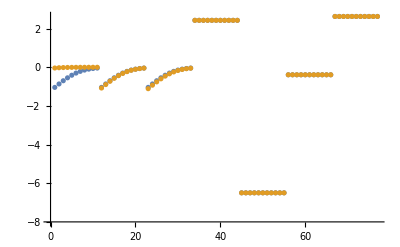

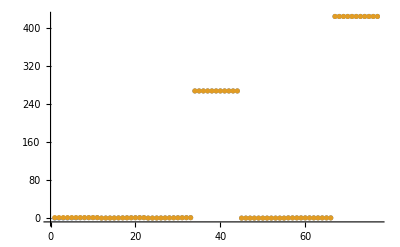

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

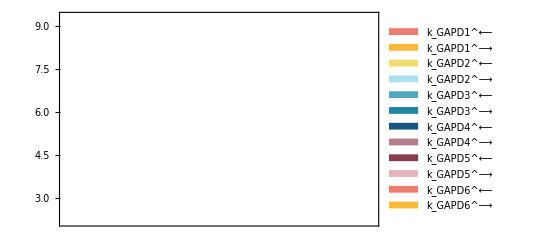

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

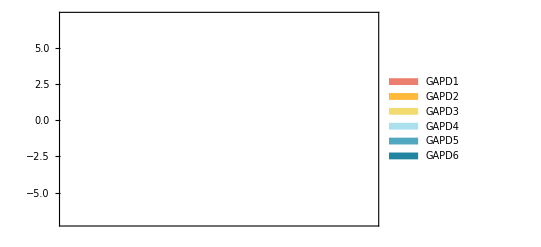

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

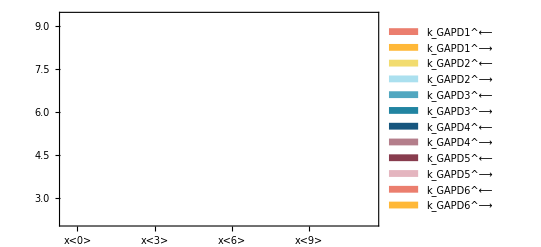

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

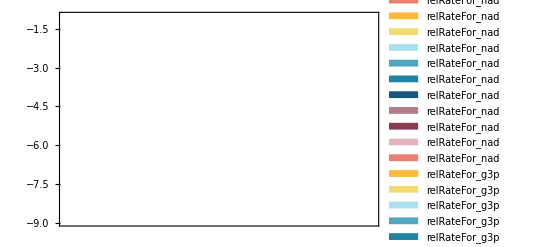

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> eTotal;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, KeqName]//TableForm
```

data value | predicted value | error in %
0.000045 | 4.07861×10^-7 | 99.0936
0.00089 | 0.000965801 | 8.51691
0.00053 | 0.000626704 | 18.246

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 0.0000142512

```mathematica
backCalculateRatios[dKdRatio, dKdVal, paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 424.997 | 0.000693463